```mathematica
(*Work in units a=1*)
(*Define regularized step function*)
st[ω_,x_]:=Exp[ω](UnitStep[x]+I Gamma[0,ω(I x+1)]/(2Pi))-Exp[-ω]I Gamma[0,ω(I x -1)]/(2Pi)
```

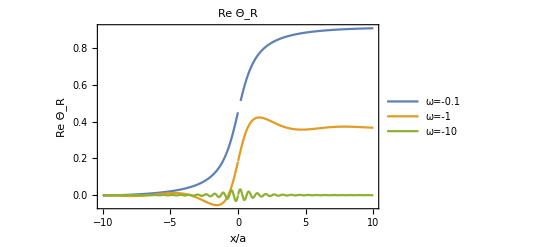

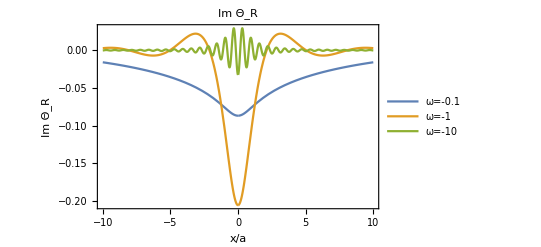

```mathematica
(*Examine regularized step function for several ω*)
p1a=Plot[{Re[st[-10^-1,x]],Re[st[-10^0,x]],Re[st[-10^1,x]]},{x,-10,10},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},PlotLabel->"Re Θ_R",Frame->True,Axes->False,FrameLabel->{"x/a","Re Θ_R"},PlotLegends->Placed[{"ω=-0.1","ω=-1","ω=-10"},{Left,Top}]]
p1b=Plot[{Im[st[-10^-1,x]],Im[st[-10^0,x]],Im[st[-10^1,x]]},{x,-10,10},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},PlotLabel->"Im Θ_R",Frame->True,Axes->False,FrameLabel->{"x/a","Im Θ_R"},PlotLegends->Placed[{"ω=-0.1","ω=-1","ω=-10"},{Left,Bottom}],PlotRange->All]
```

```mathematica
(*Self-energy: Σ(ω)=(J_⊥/2π)^2 σ(ω).*)
σ[ω_]:=Exp[ω]Gamma[0,ω+10^-10 I]-Exp[-ω]Gamma[0,-ω-10^-10 I]
```

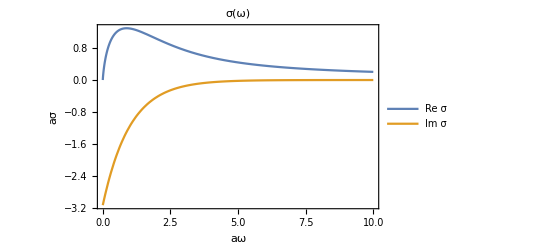

```mathematica
(*Examine σ(ω)*)
p2=Plot[{Re[σ[ω]],Im[σ[ω]]},{ω,0,10},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},PlotLabel->"σ(ω)",Frame->True,Axes->False,FrameLabel->{"aω","aσ"},PlotLegends->Placed[{"Re σ","Im σ"},{Right,Bottom}],PlotRange->All]
```

```mathematica
(*We evaluate cor=|<d^*ψ(x)>|^2 at 20 exponentially spaced points between a/2 and 700a. We define (J_⊥)^2/4π = c. We evaluate the correlator at 3 values of c, namely 1/75, 1/250 and 1/1000*) 
xarray=Table[0.5Exp[(Log[700]-Log[0.5])n/19],{n,0,19}];
carray={1/75,1/250,1/1000};
```

```mathematica
cor[c_,x_]:= Abs[NIntegrate[Exp[I ω x](st[ω,x]/(ω-c σ[ω]/Pi)-st[ω,-x]/(ω-c Conjugate[σ[ω]]/Pi))/(2Pi),{ω,-20,0},Method->"GlobalAdaptive",MaxRecursion->10]]^2
```

```mathematica
corarray=Table[{xarray[[n]],cor[carray[[m]],xarray[[n]]]},{m,1,3},{n,1,20}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in ω near {ω} = {-0.0195313}. NIntegrate obtained -0.0156144+0.000183772 ⅈ and 0.000108957 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in ω near {ω} = {-0.0195313}. NIntegrate obtained -0.044283+0.000613817 ⅈ and 0.000361354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in ω near {ω} = {-0.0195313}. NIntegrate obtained -0.12001+0.00243104 ⅈ and 0.00143032 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
(*approxcor represents the simple approximate expression we obtained for cor*)
```

```mathematica
approxcor[z_]:=(Exp[z]Gamma[0,z]/(2Pi))^2
```

```mathematica
(*compare the exact expression (solid lines) and the approximate expression (dashed lines) *)
```

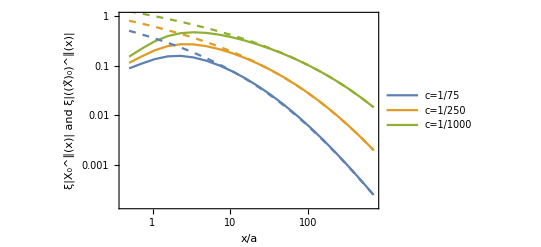

```mathematica
p3=ListLogLogPlot[corarray,Joined->True,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"x/a","ξ|X_0^∥(x)| and ξ|((X̃)_0)^∥(x)|"},PlotLegends->Placed[{"c=1/75","c=1/250","c=1/1000"},{Left,Bottom}]];
p4=LogLogPlot[{approxcor[carray[[1]]x],approxcor[carray[[2]]x],approxcor[carray[[3]]x]},{x,.5,700},PlotStyle->Dashed];
Show[p3,p4]
```